# Nanobody fits (L=144μm)

## Read data in

```mathematica
SetDirectory["/Users/hadjivz/Dropbox/Mac/Desktop/CodeOnline/Nanobody/Pent/"];
files=FileNames["dat*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
dat=Table[Import[files[[f]],"Table"],{f,1,Length[files]}]//N;
```

## Define model and fit simultaneously

From A, B, p to ks functions

```mathematica
fko := Function[{p,B, A}, p - p^2 B / (p B + A)]
fkN := Function[{p,B, A},(p B + A)]
fkr := Function[{p,B, A},p^2 B / (p B + A)]
```

Format data for simultaneous fit

```mathematica
datIndexed = Table[Table[{dat[[i,j,1]], i, dat[[i,j,2]]}, {j,1,Length[dat[[i]]]}], {i,1,Length[dat]}];
```

```mathematica
(*fitted initial intensity point (at t=0) cannot be higher than first measurement at t0>0*)
ciMax=Table[dat[[i,1,2]], {i,1,Length[dat]}];
```

Sample length up to t=4500s across experiments

```mathematica
maxT = 4500;
dat1=Table[Table[If[dat[[j,i,1]]<maxT, dat[[j,i]]], {i, 1, Length[dat[[j]]]}], {j,1,Length[dat]}];
dat2=Table[DeleteCases[dat1[[j]], Null], {j,1,Length[dat1]}];
datIndexed = Table[Table[{dat2[[i,j,1]], i, dat2[[i,j,2]]}, {j,1,Length[dat2[[i]]]}], {i,1,Length[dat2]}];
```

Fits (simultaneous)

```mathematica
modelc1:=c1(1+A t+B(1-Exp[-p t]));
modelc2:=c2(1+A t+B(1-Exp[-p t]));
modelc3:=c3(1+A t+B(1-Exp[-p t]));
modelc4:=c4(1+A t+B(1-Exp[-p t]));
modelc5:=c5(1+A t+B(1-Exp[-p t]));
modelc6:=c6(1+A t+B(1-Exp[-p t]));
modelc7:=c7(1+A t+B(1-Exp[-p t]));

modelSimultaneous[index_]:=KroneckerDelta[index-1]*modelc1+KroneckerDelta[index-2]*modelc2+KroneckerDelta[index-3]*modelc3+KroneckerDelta[index-4]*modelc4+KroneckerDelta[index-5]*modelc5+KroneckerDelta[index-6]*modelc6+KroneckerDelta[index-7]*modelc7;
```

```mathematica
ciStart = 0.1;
fitsSimultaneous=NonlinearModelFit[Flatten[datIndexed,1],{modelSimultaneous[indexi],A>0, B>0 , 0.1>p>0,
 ciMax[[1]]>c1>0,
 ciMax[[2]]>c2>0,
 ciMax[[3]]>c3>0,
 ciMax[[4]]>c4>0,
 ciMax[[5]]>c5>0,
 ciMax[[6]]>c6>0,
 ciMax[[7]]>c7>0
},{{c1,ciStart},{c2,ciStart},{c3,ciStart},{c4,ciStart},{c5,ciStart},{c6,ciStart},{c7,ciStart},{A, 0.1}, {B,30}, {p,0.01}},{t,indexi},VarianceEstimatorFunction->(Mean[Abs[#]]&)];
```

Translate (A, B, p) from fit to (ko, kN, kr) and plot fitted curves with experimental data

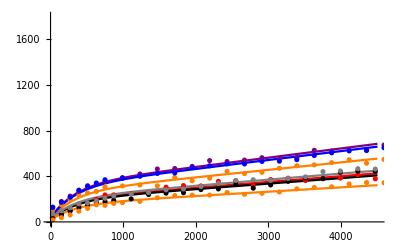

```mathematica
imin=1;
imax=13;
maxt = maxT;
maxy=1800;
imin=1;
imax=7;
Show[Plot[Evaluate@Table[modelSimultaneous[i]/.fitsSimultaneous["BestFitParameters"],{i,imin,imax}],{t,0,maxt},PlotStyle->{Orange, Red, Purple, Blue, Black, Gray},PlotRange->{{0,6000},{0,maxy}}],
ListPlot[Table[dat[[i]], {i,imin,imax}],PlotStyle->{Orange, Red, Purple, Blue, Black, Gray}],TicksStyle->Directive[Black, 14], PlotRange->{{0,maxT},{0,maxy}}]
```

```mathematica
ko=fko[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kN=fkN[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kr=fkr[p,B,A]/.fitsSimultaneous["BestFitParameters"]
```

0.000259041

0.025406

0.00267012

```mathematica
fitsSimultaneous["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c1 | 29.1528 | 1.93763 | 15.0456 | 1.47846×10^-31
c2 | 22.3918 | 1.48931 | 15.0351 | 1.57422×10^-31
c3 | 35.979 | 2.38996 | 15.0543 | 1.40459×10^-31
c4 | 34.6777 | 2.30438 | 15.0486 | 1.45265×10^-31
c5 | 21.4395 | 1.4261 | 15.0336 | 1.58795×10^-31
c6 | 23.6524 | 1.57297 | 15.0368 | 1.55867×10^-31
c7 | 16.917 | 1.12604 | 15.0234 | 1.68738×10^-31
A | 0.00224679 | 0.000154456 | 14.5464 | 2.91157×10^-30
B | 7.90644 | 0.579304 | 13.6482 | 6.51129×10^-28
p | 0.00292916 | 0.000059611 | 49.1379 | 4.01138×10^-93

Calculate s.e.m. for ko, kN, kr

```mathematica
(*variance for A, B, p from fits above*)
LOPpent={varp -> (0.00005961097609183851)^2, varA -> (0.000154455949056199)^2, varB ->(0.5793044775889263)^2, p->0.0029291571752109637,A->0.002246785719372523, B->7.906443472234678}
ParsNow=LOPpent;

(*Error propagation formula for kN*)
VarkN = varp varB + varp B^2 + varB p^2 + varA;
fskN=(D[(A+B p),A]^2 varA + D[(A+B p),B]^2 varB +  D[(A+B p),p]^2 varp );
semkn=Sqrt[fskN/.ParsNow]
```

{varp→3.55347×10^-9,varA→2.38566×10^-8,varB→0.335594,p→0.00292916,A→0.00224679,B→7.90644}

0.00176787

```mathematica
(*Error propagation formula for kr*)
fskr=(D[p^2 B/(p B + A),A]^2 varA + D[p^2 B/(p B + A),B]^2 varB +  D[p^2 B/(p B + A),p]^2 varp );
semkr=Sqrt[fskr/.ParsNow]
```

0.0000637256

```mathematica
(*Error propagation formula for ko*)
Varko = varp + varkr;
semko=Sqrt[Varko/.{varkr->fskr}/.ParsNow]
```

0.0000872606